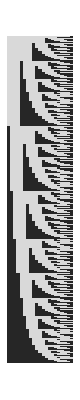
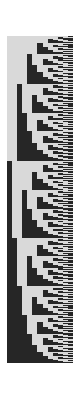
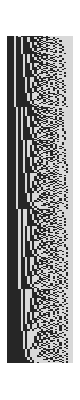
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[#,]&/@(PadRight[Sort[(StringSplit[#,""]&/@Last[ResourceFunction["MultiwaySystem"][#[[1]],#[[2]],#[[3]]]])/.{"A"->1,"B"->2}]]&/@{{{"BB"->"A","AAA"->"BB","A"->"ABA"},"BABBA",11},{{"B"->"BB","BBB"->"AAAA"},"B",20},{{"A"->"AB","B"->"A"},"A",13},{{"B"->"AA","B"->"BB"},"B",12},{{"BBAA"->"A","AB"->"BABA"},"BABBA",12}})
```